```mathematica
ClearSystemCache;
DuffingForced={x'[t]==y[t],y'[t]==x[t]-x[t]^3-0.15 y[t]+0.5 Cos[t]};
tmax=8*Pi;
AttractingWell[a_,b_]:=Sign[x[t]]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;
DensityPlot[AttractingWell[a,b],{a,-2.5,2.5},{b,-2.5,2.5},PlotPoints->50,MaxRecursion->3,Mesh->False,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[-2,2],Range[-2,2],None,None}]
```

-Graphics-

```mathematica
ClearSystemCache;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]]+0.5 Cos[t]};
tmax=8*Pi;
AttractingWell[a_,b_]:=Sign[x[t]]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax
DensityPlot[AttractingWell[a,b],{a,-2.5,2.5},{b,-2.5,2.5},PlotPoints->50,MaxRecursion->3,Mesh->False,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[-2,2],Range[-2,2],None,None}]
```

-Graphics-

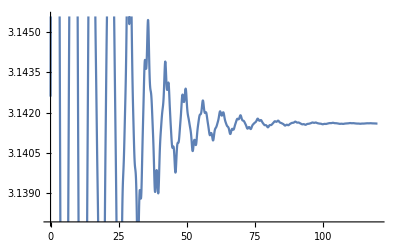

amp.25.jpg

```mathematica
ClearSystemCache;
amp=.25; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=10*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

Export["amp.25.jpg",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]]
```

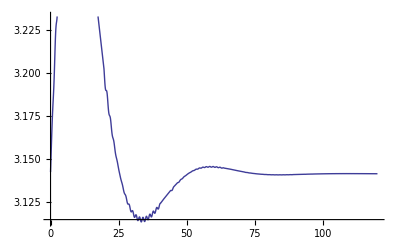

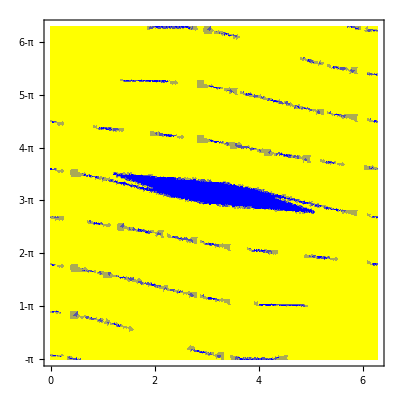

```mathematica
ClearSystemCache;
amp=.05; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=10*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

Export["belowthreshold.pdf",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]]
```

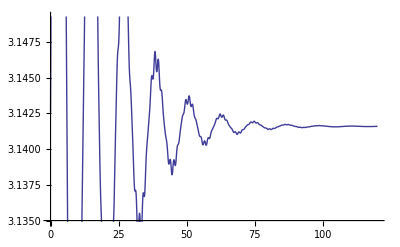

-Graphics-

```mathematica
ClearSystemCache;
amp=.15; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=10*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

BOA3=DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]
```

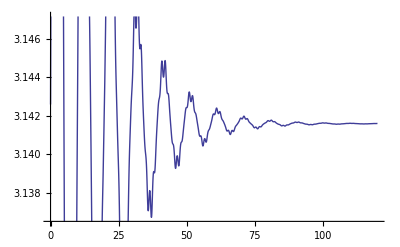

```mathematica
ClearSystemCache;
amp=.18; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=10*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

BOA3=DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]
```

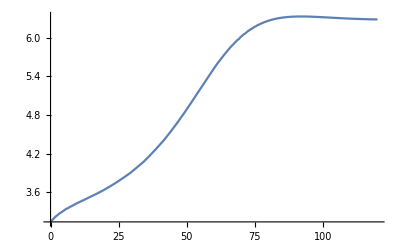

NDSolve::ndinnt: Initial condition a is not a number or a rectangular array of numbers.

ReplaceAll::rmix: Elements of {{x'[t]==y[t],y'[t]==-(0.01+0.25 Cos[«1»]) Sin[x[t]]-0.15 y[t]},x[0]==a,y[0]==b} are a mixture of lists and nonlists.

ReplaceAll::rmix: Elements of {{x'[10 π]==y[10 π],y'[10 π]==-0.26 Sin[x[Times[«2»]]]-0.15 y[10 π]},x[0]==a,y[0]==b} are a mixture of lists and nonlists.

below.jpg

```mathematica
ClearSystemCache;
amp=.01; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=10*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

Export["below.jpg",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]]
```

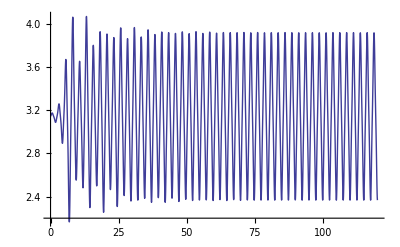

BOA.jpg

```mathematica
ClearSystemCache;
amp=.5; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=10*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

Export["BOA.jpg",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]]
```